# Connected Graph Sampler

## Prerequisites

To use the ConnectedGraphSampler package, you need:

Mathematica 10.0.2 or later.

A C++ compiler that supports the C++14 standard.

The LTemplate package. See https://github.com/szhorvat/LTemplate for installation instructions.

To check if Mathematica is already set up to use your installed C++ compiler, verify that the following does not return an empty list:

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

If LTemplate is correctly installed, evaluating the following will not result in any error messages:

```mathematica
Needs["LTemplate`"]
```

## Getting started

Add the package to the search path and load the package. The first time it is loaded, the C++ component will be automatically compiled.

```mathematica
$packagePath=FileNameJoin[{NotebookDirectory[],"."}];
If[Not@MemberQ[$Path,$packagePath],AppendTo[$Path,$packagePath]];

Get["ConnectedGraphSampler`"]
```

If compilation has failed, the most likely causes are: (1) The LTemplate package was not installed (2) No suitable C++ compiler is present on the system.

Use ? to obtain information about the symbols provided by the package:

```mathematica
?ConnectedGraphSampler`*
```

```mathematica
?CGSSample
```

CGSSample[degrees] generates a biased sample from the set of graphs with the given degrees. The result is returned in the form {graph, Log[samplingWeight]}.
CGSSample[degrees, n] generates n biased samples.
CGSSample[degrees, "Connected" -> True] samples only connected graphs.
CGSSample[degrees, "MultiEdges" -> True] allows multi-edges.
CGSSample[degrees, Exponent -> α] sets the degree affinity exponent.

## Usage

#### Basic usage

Create a single random graph with a given degree sequence. The function returns the result in the format {graph, Log[samplingWeight]}. All standard graph styling options may be used.

```mathematica
CGSSample[{3,3,2,2,1,1},
GraphStyle->"DiagramGold",VertexSize->0.6]
```

{-Graphics-,-7.67786}

Sample 6 random graphs with the given degrees.

```mathematica
degseq={3,3,2,2,2,2,2,2,1,1};
```

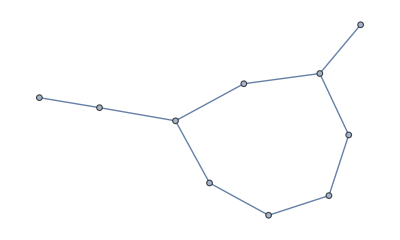
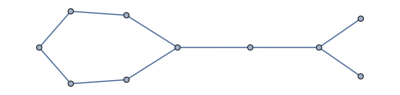
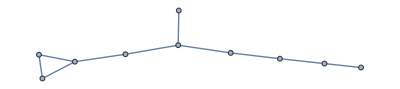
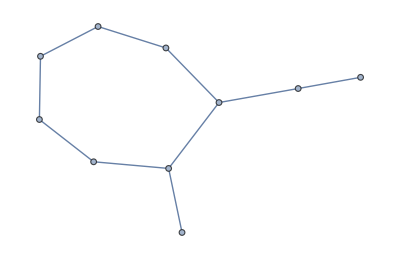
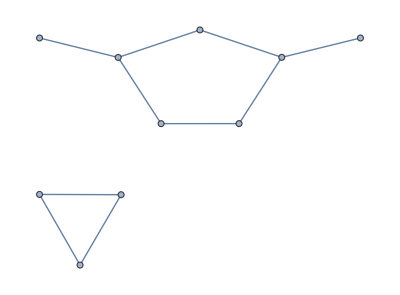
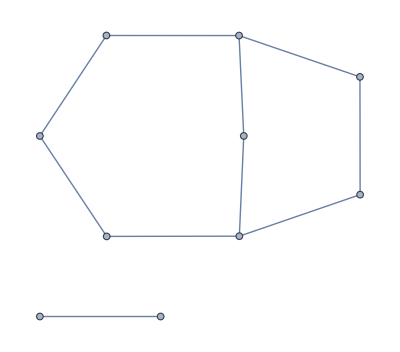
{{-Graphics-,-18.9115},{-Graphics-,-19.0293},{-Graphics-,-19.1628},{-Graphics-,-19.3502},{-Graphics-,-19.3014},{-Graphics-,-19.3012}}

```mathematica
CGSSample[degseq,6]
```

Sample loop-free multigraphs instead of simple graphs.

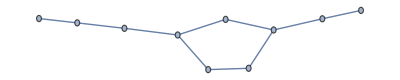
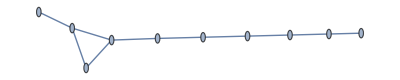
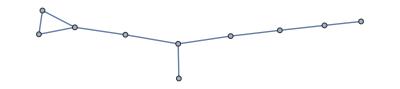
{{-Graphics-,-19.8655},{-Graphics-,-20.5587},{-Graphics-,-19.999},{-Graphics-,-19.7069},{-Graphics-,-21.1957},{-Graphics-,-19.7114}}

```mathematica
CGSSample[degseq,6,"MultiEdges"->True]
```

#### Connected graphs

Sample 6 connected graphs with the same degree sequence.

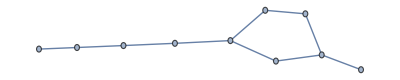
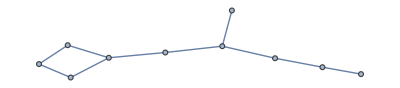
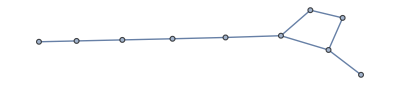
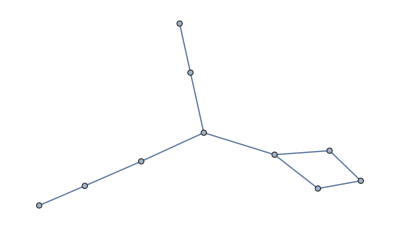
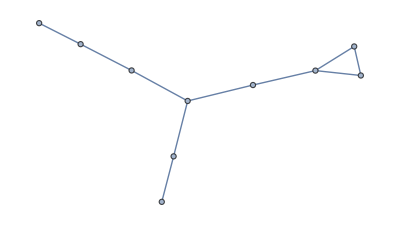
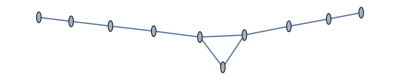
{{-Graphics-,-19.0293},{-Graphics-,-19.0983},{-Graphics-,-19.473},{-Graphics-,-18.9185},{-Graphics-,-19.2116},{-Graphics-,-18.7643}}

```mathematica
CGSSample[degseq,6,"Connected"->True]
```

Sample 6 connected loopless multigraphs.

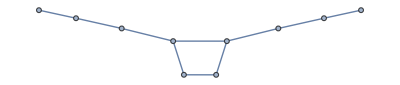
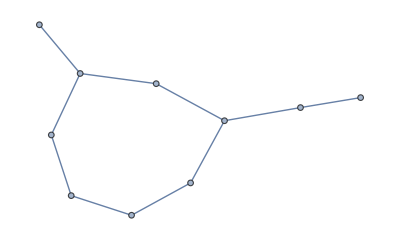
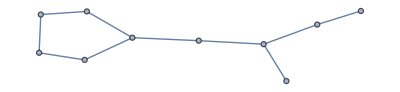
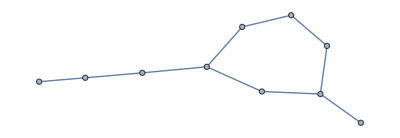
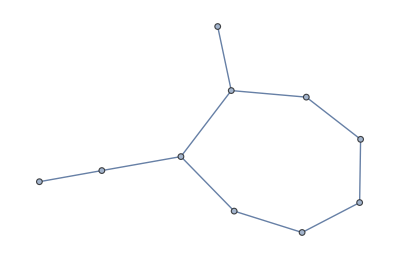
{{-Graphics-,-19.2761},{-Graphics-,-19.6424},{-Graphics-,-19.3911},{-Graphics-,-19.6424},{-Graphics-,-19.1881},{-Graphics-,-19.2651}}

```mathematica
CGSSample[degseq,6,"Connected"->True,"MultiEdges"->True]
```

#### Generating samples of numerical graph properties

Sample 1000 graphs and compute their assortativity. The result is returned as a WeightedData expression:

```mathematica
sample=CGSSampleProp[degseq,GraphAssortativity,1000]
```

WeightedData[…]

Compute the mean the standard deviation of the sample:

```mathematica
{Mean[sample],StandardDeviation[sample]}
```

{-0.174627,0.289609}

Plot the histogram of assortativity values:

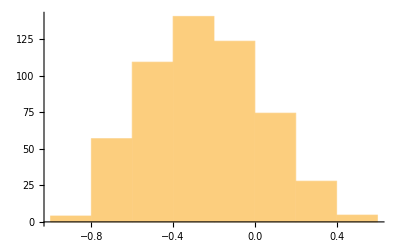

```mathematica
Histogram[sample]
```

Generate a graphical and potentially connected scale-free degree sequence;

```mathematica
SeedRandom[42]
connectedGraphicalQ=CGSPotentiallyConnectedQ[#]&&CGSGraphicalQ[#]&;
While@Not@connectedGraphicalQ[ds=Sort@RandomVariate[ZipfDistribution[1.5],100]]
```

Sample both from the set of all graphs and from the set of connected graphs, then compare the distribution of the clustering coefficient for the two cases:

```mathematica
sample1=CGSSampleProp[ds,GlobalClusteringCoefficient,10000];
sample2=CGSSampleProp[ds,GlobalClusteringCoefficient,10000,"Connected"->True];
```

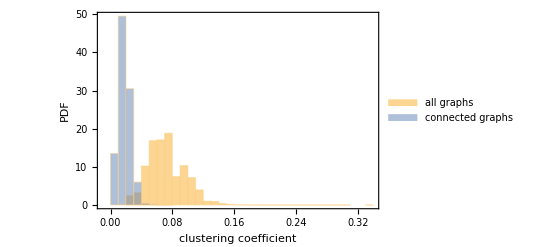

```mathematica
Histogram[{sample1,sample2},{0.01},"PDF",
Frame->True,FrameLabel->{"clustering coefficient","PDF"},
ChartLegends->{"all graphs","connected graphs"}]
```

Plot the histogram of the natural logarithm of sampling weights:

```mathematica
weights1=CGSSample[ds,10000]⟦All,2⟧;
weights2=CGSSample[ds,10000,"Connected"->True]⟦All,2⟧;
```

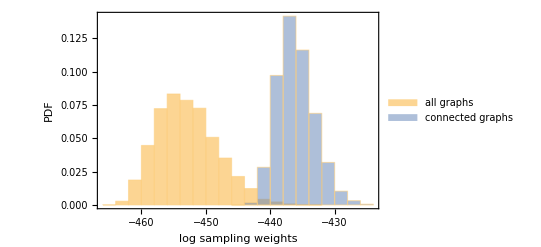

```mathematica
Histogram[{weights1,weights2},Automatic,"PDF",
Frame->True,FrameLabel->{"log sampling weights","PDF"},
ChartLegends->{"all graphs","connected graphs"}]
```

#### Generate all realizations

Let us generate a very large sample for a small degree sequence.

```mathematica
samp=CGSSample[{3,3,2,2,1,1},100000];
```

Visualize the fraction of times each realization is generated, i.e. the biased sampling distribution.

```mathematica
countsPlot[asc_]:=
BarChart[asc,
ChartLabels->Placed[Automatic,Below,Rotate[AdjacencyGraph[#,ImageSize->30,VertexSize->Large],Pi/2]&],
ImageSize->Large,AspectRatio->1/3
]
```

```mathematica
samp[[All,1]]//CountsBy[AdjacencyMatrix]//KeySort//Normalize[#,Total]&//countsPlot
```

-Graphics-

“Ubias” the result and verify that it is uniform.

```mathematica
samp//GroupBy[AdjacencyMatrix@*First->Last]//KeySort//Exp[-#]&//Map[Total]//Normalize[#,Total]&//countsPlot
```

-Graphics-

Repeat the computations from above for only connected realizations.

```mathematica
csamp=CGSSample[{3,3,2,2,1,1},100000,"Connected"->True];
```

```mathematica
csamp[[All,1]]//CountsBy[AdjacencyMatrix]//KeySort//Normalize[#,Total]&//countsPlot
```

-Graphics-

```mathematica
csamp//GroupBy[AdjacencyMatrix@*First->Last]//KeySort//Exp[-#]&//Map[Total]//Normalize[#,Total]&//countsPlot
```

-Graphics-

## Common options

All sampling functions in this package accept the following options:

"Connected"→True will sample only connected graphs.

"MultiEdges"→True will sample loop-free multigraphs instead of simple graphs (which is the default).

RandomSeeding→Automatic will auto-seed the graph sampler using Mathematica’s own random number generator. This is the default. RandomSeeding→1234 will use 1234 as the seed.

Exponent→α will connect the current stub to a vertex of remaining degree d with probability proportional to d^α. Equivalently, the current stub is connected to a stub that belong to a vertex of degree d with probability proportional to d^(α-1). The default is α=1, i.e. stubs to connect to are chosen uniformly.